```mathematica
(* deriving Newton force using dipole ansatz for tiny twists of 0th time axis *)
```

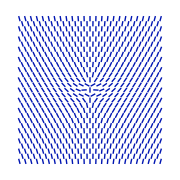
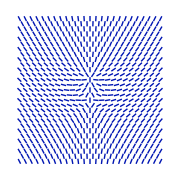
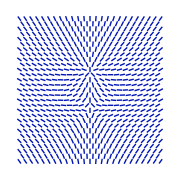
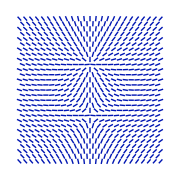
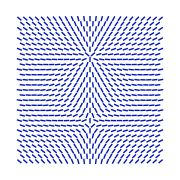
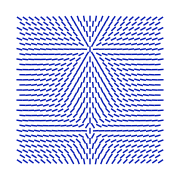

```mathematica
cos=1+(z-d)/Sqrt[(z-d)^2+r^2]-(z+d)/Sqrt[(z+d)^2+r^2];              (* Manfried Faber dipole ansatz *)
n={Sqrt[1-cos^2]x/r,Sqrt[1-cos^2]y/r,cos}/.r->Sqrt[x^2+y^2];                          (* vector field - here of deformation of time axis directions *)
Table[VectorPlot[n[[{1,3}]]/.y->0,{x,-2,2},{z,-2,2},VectorMarkers-> "Segment",VectorPoints->Fine,Frame->False,ImageSize->Small],{d,0.1,1.1,0.2}]//Row
```

```mathematica
G=Table[t=Table[0,4,4];t[[1,i]]=-1;t[[i,1]]=1;t,{i,2,4}]; (* 4d rotation generators *)
M0={{g,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}};          (* rest field for {g,1,0,0} axes lengths *)
o=MatrixExp[m*{a,b,c}.G];                       (* m is the mass - it is tiny, we focus on Taylor to m^1 *)
M=Series[o.M0.Transpose[o]/.{a->n[[1]],b->n[[2]],c->n[[3]]},{m,0,1}]//Normal//Simplify
```

{{g,((-1+g) m x √(1-(1+(-d+z)/(√(x^2+y^2+(d-z)^2))-(d+z)/(√(x^2+y^2+(d+z)^2)))^2))/(√(x^2+y^2)),(g m y √(1-(1+(-d+z)/(√(x^2+y^2+(d-z)^2))-(d+z)/(√(x^2+y^2+(d+z)^2)))^2))/(√(x^2+y^2)),g m (1-d/(√(d^2+x^2+y^2-2 d z+z^2))+z/(√(d^2+x^2+y^2-2 d z+z^2))-d/(√(d^2+x^2+y^2+2 d z+z^2))-z/(√(d^2+x^2+y^2+2 d z+z^2)))},{((-1+g) m x √(1-(1+(-d+z)/(√(x^2+y^2+(d-z)^2))-(d+z)/(√(x^2+y^2+(d+z)^2)))^2))/(√(x^2+y^2)),1,0,0},{(g m y √(1-(1+(-d+z)/(√(x^2+y^2+(d-z)^2))-(d+z)/(√(x^2+y^2+(d+z)^2)))^2))/(√(x^2+y^2)),0,0,0},{g m (1-d/(√(d^2+x^2+y^2-2 d z+z^2))+z/(√(d^2+x^2+y^2-2 d z+z^2))-d/(√(d^2+x^2+y^2+2 d z+z^2))-z/(√(d^2+x^2+y^2+2 d z+z^2))),0,0,0}}

```mathematica
(* take lowest m power: m^4  *)
```

```mathematica
dM={D[M,x],D[M,y],D[M,z]};
H=Coefficient[Sum[Total[(dM[[i]].dM[[j]]-dM[[j]].dM[[i]])^2,2],{i,2},{j,i+1,3}]/.y->0,m^4]//FullSimplify
```

1/((d^4+2 d^2 (x-z) (x+z)+(x^2+z^2)^2)^3)4 g^2 (d^4-(x^2+z^2) (-x^2-z^2+√(x^2+(d-z)^2) √(x^2+(d+z)^2))+d^2 (2 x^2+6 z^2+√(x^2+(d-z)^2) √(x^2+(d+z)^2))) (d^4 (3+(-6+g) g)+(-1+g)^2 x^4+2 d^3 (-1+2 g) (√(x^2+(d-z)^2)+√(x^2+(d+z)^2))+2 d (-1+2 g) (x-z) (x+z) (√(x^2+(d-z)^2)+√(x^2+(d+z)^2))+2 x^2 z ((2+(-4+g) g) z-(-1+2 g) (√(x^2+(d-z)^2)-√(x^2+(d+z)^2)))+z^2 ((3+(-6+g) g) z^2+2 (-1+2 g) √(x^2+(d-z)^2) √(x^2+(d+z)^2)-2 (-1+2 g) z (√(x^2+(d-z)^2)-√(x^2+(d+z)^2)))+2 d^2 ((2+(-4+g) g) x^2-(3+(-6+g) g) z^2+(1-2 g) √(x^2+(d-z)^2) √(x^2+(d+z)^2)+(-1+2 g) z (√(x^2+(d-z)^2)-√(x^2+(d+z)^2))))

```mathematica
CoefficientList[H,g]//Length
```

5

```mathematica
(* focus on the highest g power: g^4 *)
```

```mathematica
HH=FullSimplify[CoefficientList[H,g][[-1]]]
```

(4 (d^4-(x^2+z^2) (-x^2-z^2+√(x^2+(d-z)^2) √(x^2+(d+z)^2))+d^2 (2 x^2+6 z^2+√(x^2+(d-z)^2) √(x^2+(d+z)^2))))/((d^4+2 d^2 (x-z) (x+z)+(x^2+z^2)^2)^2)

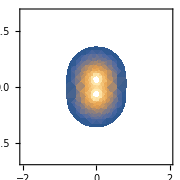
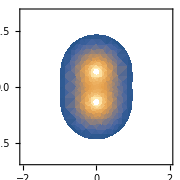
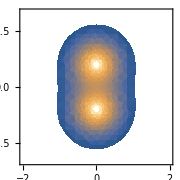
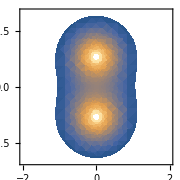
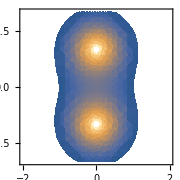
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Table[DensityPlot[Log[HH],{x,-2,2},{z,-2,2},PlotRange->{0,10},ImageSize->Small],{d,0.,1,0.2}]//Row
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1589.56-25.1609/d

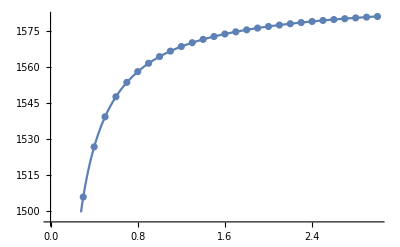

```mathematica
fr=0.1;to=3;st=0.1;
Es=Table[{d,NIntegrate[4Pi*x*HH*Boole[x^2+(z-d)^2>0.001],    
{x,0,Infinity},{z,0,Infinity}]},{d,fr,to,st}]; (*integrate H: total field energy*)
Print[ft=Fit[Es,{1,1/d},d]]; Show[ListPlot[Es],Plot[ft,{d,fr,to}]]
```